# Classical Mechanics and Complex Numbers

## Purpose

The purpose of this lesson is to...

provide a reminder of some concepts from classical mechanics that will be important in this course.

introduce the concept of Hamiltonian mechanics, which will be very important for our conceptualization of quantum mechanics.

review the concept of complex numbers, the complex plane, and Euler’s formula.

## Learning Objectives

At the end of this lesson, I should be able to...

apply Newton’s equations of motion to describe the force balance acting on a system.

describe a classical system using Hamiltonian mechanics instead of Newtonian mechanics.

describe imaginary numbers and the complex plane.

apply the Euler formula to describe sinusoidal (cyclic) functions in the complex plane.

## Newtonian and Hamiltonian Mechanics

### Reminder - working with derivatives and partial derivatives

In case you haven’t worked with partial derivatives in a while, let’s briefly review some concepts. 

A derivative, recall, just tells us how a function changes with respect to a variable. So for example, if f(t)  gives the position as a function of time

(ⅆf(t))/ⅆt=v(t)

where v is the velocity. So the derivative gives us the change in position with respect to time, or velocity. If we take the second derivative,

(ⅆ^2 f(t))/(ⅆ t^2)=(ⅆv(t))/ⅆt=a(t)

we get the acceleration a. So the second derivative tells us the rate of change in the rate of change of the position, or the rate of change in the velocity, which is the acceleration rate.

So now, if we have a function of two variables, u (x, t ), and we take a partial derivative,

(∂^2 u(x,t))/(∂t^2)

that describes only how the function u changes with time for a given position (specifically, this second partial derivative tells us the rate of change in the rate of change of u). It doesn’t tell us how the function u changes with position.

### Simple pendulum - Newtonian mechanics

We will use the pendulum as a demonstrative system for explaining the process of analysis with Newtonian mechanics. Consider a pendulum comprising a string of length l attached to a fixed point at one end and to a mass m at the other end. We will designate the vertical coordinate as y, and the horizontal coordinate as x. Another important descriptor of this system is the angle θ, which describes the angle between the string and the y axis (see Figure 0.1). Additionally, we can describe the arclength s, which gives the path of displacement of the pendulum mass from its resting position, using

θ=s/l

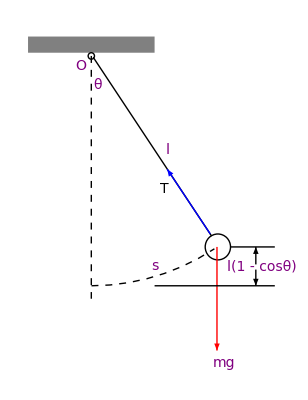

```mathematica
polygon=Polygon[{{-1,0},{1,0},{1,1/4},{-1,1/4}}];
top=Graphics[{Gray,polygon}];
circle1=Graphics[Circle[{0,-1/20},1/20]];
circle2=Graphics[Circle[{2,-3},1/5]];
circle3=Graphics[{Dashed,Circle[{0,0},3.6,{-1.57,-1.0}]}];
line1=Graphics[{Dashed,Line[{{0,-1/20},{0,-3.8}}]}];
line2=Graphics[{Thick,Line[{{0.03,-0.07},{1.9,-2.83}}]}];
arrow=Graphics[{Red,Arrowheads[0.08],Arrow[{{1.986,-3.0},{1.986,-4.6}}]}];
line3=Graphics[{Line[{{2.2,-3.8},{2.9,-3.8}}]}];
arrow2a=Graphics[{Arrowheads[0.04],Arrow[{{0.7,-3.8},{0,-3.8}}]}];
arrow2b=Graphics[{Arrowheads[0.04],Arrow[{{1.3,-3.8},{1.98,-3.8}}]}];
text1=Graphics[Text[Style["s",FontSize->14,Purple],{1.0,-3.3}]];
text2=Graphics[Text[Style["mg",FontSize->14,Purple],{2.1,-4.8}]];
line3=Graphics[{Line[{{1.0,-3.6},{2.9,-3.6}}]}];
line4=Graphics[{Line[{{2.2,-3.0},{2.9,-3.0}}]}];
text3=Graphics[Text[Style["l(1 - cosθ)",FontSize->14,Purple],{2.7,-3.3}]];
arrow3a=Graphics[{Arrowheads[0.04],Arrow[{{2.6,-3.35},{2.6,-3.6}}]}];
arrow3b=Graphics[{Arrowheads[0.04],Arrow[{{2.6,-3.27},{2.6,-3.0}}]}];
text4=Graphics[Text[Style["l",FontSize->14,Purple],{1.2,-1.5}]];
text5=Graphics[Text[Style["θ",FontSize->14,Purple],{0.1,-0.5}]];
text6=Graphics[Text[Style["O",FontSize->14,Purple],{-0.16,-0.2}]];
textT=Graphics[Text[Style["T",FontSize->14,Black],{1.15,-2.1}]];
arrowT=Graphics[{Blue,Arrowheads[0.08],Arrow[{{1.88,-2.8},{1.2,-1.8}}]}];
Show[top,circle1,circle2,circle3,line1,line2,arrow,text1,text2,text4,text5,text6,arrowT,textT, line3,line4,text3,arrow3a,arrow3b]
```

Figure 0.1. Simple pendulum model. Adapted from Prof. Vladimir Dobrushkin, Brown University, https://www.cfm.brown.edu/people/dobrush/am33/Mathematica/ch4/simple.html

In Newtonian mechanics, we wish to describe the system based on the forces acting on it, so we need to identify those forces. Neglecting any damping of the oscillation from friction, the only forces are gravity mg, which points down on the mass at all points, and tension T, which points along the string from the mass to the origin. According to Newton’s second law, we can then sum up those forces and set them equal to ma. We will find that the net force along the direction of travel will be the component of mg that is perpendicular to T . As the pendulum moves, the magnitude of this component changes, but we can define this using a bit of geometry to be

-m g sin(θ)

where the negative sign indicates that this force points in the opposite direction of displacement. Then, because this force is only pointing in the direction of the arc, we can write the acceleration to only be in the s direction,

F=ma=m(ⅆ^2 s)/(ⅆ t^2)

Setting these two equivalent descriptions equal to one another yields

m(ⅆ^2 s)/(ⅆ t^2)=-m g sin(θ)

Then, using equation (4), we obtain

(ⅆ^2 θ)/(ⅆ t^2)=-g/l sin(θ)

For small angles, we can use the approximation

θ ≈sin(θ)

to give

(ⅆ^2 θ)/(ⅆ t^2)+g/l θ=0

This equation describes simple harmonic motion and has a highly characteristic form of solution. We will return to solving these types of equations later in the course, but the solutions take the form

θ(t)=θ_0 cos(ωt)

Where θ_0 is the initial angle of displacement, and the angular frequency of oscillation ω is given by

ω=√(g/L)

The evolution of the forces on the pendulum can be visualized in Figure 0.2

Figure 0.2. Forces on a Pendulum. Bernard Vuilleumier  (March 2011), CC BY-NC-SA 3.0, Wolfram Demonstrations Project, https://demonstrations.wolfram.com/ForcesOnAPendulum/

### Simple Pendulum - Hamiltonian mechanics

We can also describe our pendulum system using an alternate formulation known as Hamiltonian mechanics. In this approach, we first want to identify the Hamiltonian for the system, which (in the cases we care about) is the sum of the kinetic energy T and the potential energy V,

H=T+V

For the simple pendulum, the kinetic energy is given by

T=1/2 mv^2=1/2 m (ⅆs/ⅆt)^2=1/2 ml^2(ⅆθ/ⅆt)^2

where we have used equation (4) in the last transformation again.

The potential energy of the pendulum, using the lowest point in the arc as y=0, is given by

V=mgy=mgl[1-cos(θ)]

(see Figure 0.1)

Finally, we need to note that the momentum of this system is given by

p=ml^2 ⅆθ/ⅆt

We have have the Hamiltonian for this system

H=1/2 ml^2(ⅆθ/ⅆt)^2+mgl[1-cos(θ)]

which we could also write as

H=p^2/(2 ml^2)+mgl[1-cos(θ)]

The system is then described by Hamilton’s equations,

(∂θ)/(∂t)=(∂H)/(∂p)

(∂p)/(∂t)=-(∂H)/(∂θ)

If we plug equation (18) into equation (19), we obtain

ⅆθ/ⅆt=p/ml^2

and doing the same for equation (18) into equation (20), we get

ⅆp/ⅆt=-mgl sin(θ)

then taking the derivative of equation (21) with respect to t, we obtain

(ⅆ^2 θ)/(ⅆ t^2)=1/ml^2(ⅆp/ⅆt)

or

ⅆp/ⅆt=ml^2(ⅆ^2 θ)/(ⅆ t^2)

Setting the two expressions for ⅆp/ⅆtequal, we end up with

ml^2(ⅆ^2 θ)/(ⅆ t^2)=-mgl sin(θ)

Then, eliminating common factors yields

l(ⅆ^2 θ)/(ⅆ t^2)=-g sin(θ)

or

(ⅆ^2 θ)/(ⅆ t^2)+(g/l) sin(θ)=0

which is exactly the same as equation (8) that we obtained by Newtonian mechanics!

#### Takeaways from Hamiltonian mechanics

If you haven’t worked with Hamiltonian mechanics before, the previous section may have been a bit confusing. The takeaways that are important for this class moving forward are

Equivalent to a Newtonian (force-based) description of a system, we can use a Hamiltonian description that involves the sum of kinetic and potential energies.

There is a relationship between the kinetic energy term and the momentum of the system.

Either description provides the same result for the evolution of the system in time.

## Complex numbers - a review

### The “Imaginary” Number

The imaginary number, which we will call ⅈ but is also referred to as ⅉ, is defined as

ⅈ^2=−1

But why would we ever need such a number? Well, if you want to solve the roots of the equation

x^2+1=0

you get

x=±√(−1)

or

x=±ⅈ

### The Complex Plane

We want to talk about the combination of imaginary numbers and what we call real numbers (the numbers you are more accustomed to). When we combine a real number x with an imaginary number ⅈy, we get a complex number z given by

z=x+ⅈy

We also need to note some properties of complex numbers that hopefully you can visualize if you think about the complex plane. If you add complex numbers, then you just add their real and imaginary parts

z_1+z_2=(x_1+x_2)+ⅈ(y_1+y_2)

We can visualize the value z_1+z_2 in a plot as the addition of two vectors

(2+4ⅈ)+(1−3ⅈ)=(2+1)+ⅈ(4−3)=3+ⅈ

as shown in Figure 0.3.

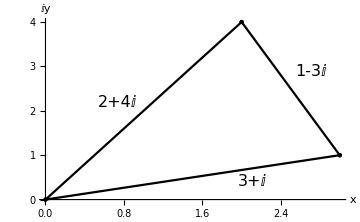

```mathematica
ComplexListPlot[{{0,2+4I},{2+4I,3+I},{0,3+I}}, BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"x","ⅈy"},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Joined->True,Mesh->All,PlotLabels->Placed[{"2+4ⅈ","1-3ⅈ","3+ⅈ"},{{0.75,2},{2.7,2.7},{2.1,0.6}}],ImageSize->Medium,AspectRatio->1/GoldenRatio]/.Line->Arrow
```

Figure 0.3. Vector addition in the complex plane.

### The Complex Conjugate

The complex conjugate is a concept that we will encounter frequently in this course. For a complex number z,

z=x+ⅈy

the complex conjugate z^⋆ is defined as

z^⋆=x−ⅈy

This concept will be important later on.

### Polar Coordinates and the Complex Plane

If we want to instead multiply two complex numbers, then things are a bit more complicated

z_1 z_2=(x_1+ⅈy_1)(x_2+ⅈy_2)
	=(x_1 x_2−y_1 y_2)+ⅈ(x_1 y_2+x_2 y_1)

We can’t really easily represent this equation using the vector approach we used for addition. But we can transform to polar coordinates using some trigonometric identities, as represented visually in Figure 0.4.

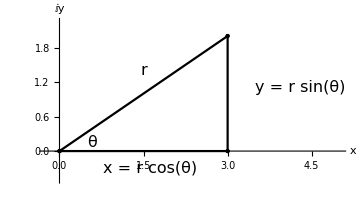

```mathematica
ComplexListPlot[{{0,3+2I},{3,3+2I},{0,3},{0}}, BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"x","ⅈy"},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Joined->True,Mesh->All,Ticks->None,PlotLabels->Placed[{"x = r cos(θ)","y = r sin(θ)","r","θ"},{{1.5,-0.1},{3.536,1.1},{1.5,1.2},{0.45,0.15}}],PlotRange->{{-0.25,5},{-0.5,2.25}},ImageSize->Medium,AspectRatio->Automatic]
```

Figure 0.4. Trigonometric identities in the complex plane.

So now we can represent the complex number z as

z=x+ⅈy=r(cos θ+ⅈ sin θ)

and we can convert our product z_1 z_2 to a form that is easier to understand

z_1 z_2=r_1(cos θ_1+ⅈ sin θ_1)r_2(cos θ_2+ⅈ sin θ_2)
	=r_1 r_2[(cos θ_1 cos θ_2− sin θ_1 sin θ_2)+ⅈ(sin θ_1 cos θ_2+cos θ_1 sin θ_2)]

using our sum/difference trigonometric identities, this converts to

z_1 z_2=r_1 r_2[cos (θ_1+θ_2)+ⅈ sin(θ_1+θ_2)]

so when we multiply complex numbers, we multiply the “radii” (called the moduli) and add the “angles” (called the phases).

### Euler’s Formula

Now, let’s go back to the case of a complex number in polar coordinates

z=r(cos θ+ⅈ sin θ)

If we think about the case where r  = 1, then by just changing θ, we go around in a circle on the complex plane of radius 1, as illustrated in Figure 0.5.

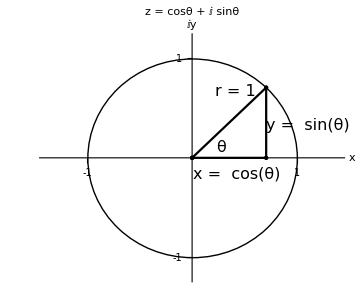

```mathematica
ComplexListPlot[{{0,(1+ⅈ)/(√2)},{0,1/(√2)},{1/(√2),(1+ⅈ)/(√2)},{0}},Prolog->{Circle[]},PlotRange->{{-1.4,1.4},{-1.2,1.2}}, BaseStyle->{FontFamily->"Arial",FontSize->16},PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{"x","ⅈy"},AxesStyle->Directive[Thick,Black],TicksStyle->Directive[Black, Thick],Ticks->{{-1,1},{-1,1}},Joined->True,Mesh->All,PlotLabels->Placed[{"x =  cos(θ)","y =  sin(θ)","r = 1","θ"},{{0.4,-0.05},{1.1,0.2},{0.42,0.55},{0.2,0.1}}],PlotRange->{{-0.25,5},{-0.5,2.25}},ImageSize->Medium,AspectRatio->Automatic,PlotLabel->Style["z = cosθ + ⅈ sinθ", 16, Black]]
```

Figure 0.5. Illustration of movement along a circle in the complex plane. Change the value of θ in z=r(cos θ+ⅈ sin θ) moves along a circle of radius r in the complex plane.

It turns out that there is an alternate form of representing a point on a circle in the complex plane that we will use frequently in this course. Remember that when we multiply two complex numbers,

z_1 z_2=r_1 r_2[cos (θ_1+θ_2)+ⅈ sin(θ_1+θ_2)]

so when r = 1, we just add the angles to move around the unit circle.

If we consider that exponents also add when multiplied, i.e.,

a^θ_1 a^θ_2=a^(θ_1+θ_2)

perhaps we can represent our sin/cos equation using an exponent.  From here, the math gets a bit complicated, but we find that the proper equation is

ⅇ^(±ⅈθ)=cos θ± ⅈ sin θ

This is known as Euler’s formula, and it is an extremely important tool in quantum mechanics. We’ll be using it quite often as the course goes on.